# File Writer and Time Tagger Virtual

## Initialization

## Establish .NET connection

```mathematica
Needs["NETLink`"];
(* load NETLink package to create a .NET context *)
InstallNET[];
(* launch the .NET runtime and prepare it to be used from Mathematica *)
TimeTagger=LoadNETAssembly["SwabianInstruments.TimeTagger"];
(* load the SwabianInstruments.TimeTagger assembly into the .NET runtime *) 
(* return to TimeTagger the expression that can be used to identify the assembly *)
TT=NETNew["SwabianInstruments.TimeTagger.TT"];
(* construct a new .NET object TT of type "SwabianInstruments.TimeTagger.TT" *)
```

## Create a Time Tagger instance

```mathematica
tagger=TT@createTimeTagger[];
(* create Time Tagger instance with the name tagger *)
(* alternative synthex: TT[createTimeTagger[]] *)
```

## Utilities

```mathematica
(*** Functions converting time to ps for Time Tagger ***)
ps[t_]:=t;
ns[t_]:=t*10^3;
us[t_]:=t*10^6;
ms[t_]:=t*10^9;
s[t_]:=t*10^12;
(* Example: ms[1] or 1//ms equals to 1*1E9 *)
```

## Measurements using physical channels

## Demonstrate File Writer with Test Signal

Enable test signal on channels 1 and 2 and record the time tags to .ttbin-files in the current directory.

```mathematica
channels={1,2};
tagger@setTestSignal[channels,True];
(* enable a test signal at the channels 1 and 2 *)
filename=NotebookDirectory[]<>"file_writer_data.ttbin";
(* If you with so save the output elswhere, modify the path accordingly *)
fw=NETNew["SwabianInstruments.TimeTagger.FileWriter", tagger,filename ,channels];
(* initialize the File Writer like any other measurement class *)
(* at this point, File Writer autostarts and creates a "file_writer_data.ttbin" header file *)
fw@startFor[10//s];
(* run the File Writer for a certain time *)
(* File Writer is going to create "file_writer_data.1.ttbin" and "file_writer_data.2.ttbin" files in the current directory*)
While[fw@isRunning[],Pause[0.1]];
(* wait until the writing is done *)
tagger@setTestSignal[channels,False];
(* disable the test signals at the channels 1 and 2 *)
TT@freeTimeTagger[tagger];
(* release the Time Tagger *)
```

## Replay using Virtual Time Tagger

## Demonstrate Virtual Time Tagger with the recorded signal

Take the .ttbin-files from the current directory and measure correlation for the previously recorded tags.

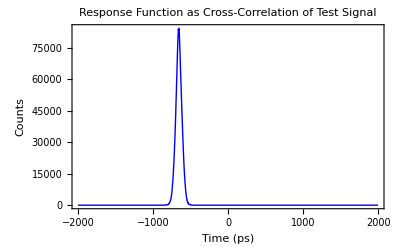

```mathematica
virttagger=TT@createTimeTaggerVirtual[];
(* create a Virtual Time Tagger instance with the name virttagger *)
binwidth=1//ps;
nbins=4*10^3;
corr=NETNew["SwabianInstruments.TimeTagger.Correlation",virttagger,channels⟦1⟧,channels⟦2⟧,binwidth,nbins];
(* pass the virttagger as an argument for any measurement class - here Correlation*)
speed=20.0;
virttagger@setReplaySpeed[speed];
(* set an arbitrary replay speed if needed *)
(* by default, the data are replayed at the same speed as they have been acquired *)
filename=NotebookDirectory[]<>"file_writer_data.ttbin";
begin=0//ps;(* duration in ps to skip at the beginning of the file *)
duration=-1; (* replay everything; alternatively - duration in ps to replay *)
virttagger@replay[filename,begin, duration];
virttagger@waitForCompletion[];
(* wait till the Virtual Time Tagger replays the recorded data completely *)
(*** Plot the resulting correlation ***)
xcorr= corr@getIndex[];
(* array of time indexes in ps from the "corr" measurement *)
ycorr  = corr@getData[];
(* array of y-values from "corr" measurement *)
corrData=Table[{xcorr⟦i⟧,ycorr⟦i⟧},{i,1,Length[xcorr]}];
(* create table of {x,y} values for plotting and export *)
ListLinePlot[corrData,Frame->True,PlotRange-> Full, PlotStyle->{{Thick,Blue}}, FrameLabel-> {"Time (ps)", "Counts"}, PlotLabel->"Response Function as Cross-Correlation of Test Signal"]
(* plot the cross-correlation function *)
```